```mathematica
Table1=({{"Element", "Z", "λ_K_α", "λ_K_β", "E_K_α", "E_K_β", "√(E_K_α/Ry)", "√(E_K_β/Ry)"}, {"Ti", 0, 2749.9, 2514.9, 0, 0, 0, 0}, {"V", 0, 2505, 2285, 0, 0, 0, 0}, {"Cr", 0, 2291.1, 2086, 0, 0, 0, 0}, {"Mn", 0, 2104, 1911.0, 0, 0, 0, 0}, {"Fe", 0, 1937, 1757, 0, 0, 0, 0}, {"Ni", 0, 1658, 1500.1, 0, 0, 0, 0}, {"Cu", 0, 1540, 1390, 0, 0, 0, 0}, {"Ag", 0, 560, 500, 0, 0, 0, 0}, {"Mo", 0, 711, 632, 0, 0, 0, 0}, {"Nb", 0, 748, 666, 0, 0, 0, 0}});
For[i=2,i≤Length[Table1],i++,
Table1[[i,2]]=ElementData[Table1[[i,1]],"AtomicNumber"];
Table1[[i,3]]=Quantity[Table1[[i,3]],"Milliangstroms"];
Table1[[i,4]]=Quantity[Table1[[i,4]],"Milliangstroms"];
Table1[[i,5]]=N[Quantity[12398000,"Electronvolts"*"Milliangstroms"]/Table1[[i,3]]];
Table1[[i,6]]=N[Quantity[12398000,"Electronvolts"*"Milliangstroms"]/Table1[[i,4]]];
Table1[[i,7]]=√(Table1[[i,5]]/Quantity[1,"Rydbergs"]);
Table1[[i,8]]=√(Table1[[i,6]]/Quantity[1,"Rydbergs"]);
]
Table1//TableForm
```

Element | Z | λ_K_α | λ_K_β | E_K_α | E_K_β | √(E_K_α/Ry) | √(E_K_β/Ry)
Ti | 22 | 2749.9 mÅ | 2514.9 mÅ | 4508.53 eV | 4929.82 eV | 18.2036 | 19.0351
V | 23 | 2505 mÅ | 2285 mÅ | 4949.3 eV | 5425.82 eV | 19.0727 | 19.9697
Cr | 24 | 2291.1 mÅ | 2086 mÅ | 5411.37 eV | 5943.43 eV | 19.9431 | 20.9006
Mn | 25 | 2104 mÅ | 1911. mÅ | 5892.59 eV | 6487.7 eV | 20.811 | 21.8366
Fe | 26 | 1937 mÅ | 1757 mÅ | 6400.62 eV | 7056.35 eV | 21.6896 | 22.7735
Ni | 28 | 1658 mÅ | 1500.1 mÅ | 7477.68 eV | 8264.78 eV | 23.4435 | 24.6465
Cu | 29 | 1540 mÅ | 1390 mÅ | 8050.65 eV | 8919.42 eV | 24.3251 | 25.604
Ag | 47 | 560 mÅ | 500 mÅ | 22139.3 eV | 24796. eV | 40.3387 | 42.6904
Mo | 42 | 711 mÅ | 632 mÅ | 17437.4 eV | 19617.1 eV | 35.7998 | 37.9714
Nb | 41 | 748 mÅ | 666 mÅ | 16574.9 eV | 18615.6 eV | 34.9032 | 36.9895

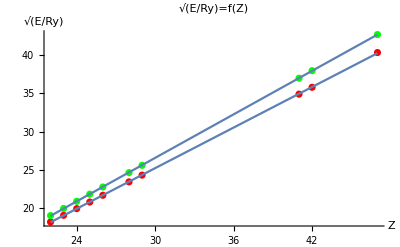

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.27391 | 0.0495469 | -25.7112 | 5.616×10^-9
x | 0.883614 | 0.00155374 | 568.702 | 1.02353×10^-19

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.84261 | 0.0291086 | -63.3012 | 4.31324×10^-12
x | 0.947373 | 0.000912814 | 1037.86 | 8.31948×10^-22

```mathematica
PlotData1=Transpose[{Table1[[2;;All,2]]}].({{1, 0}})+Transpose[{Table1[[2;;All,7]]}].({{0, 1}});
PlotData2=Transpose[{Table1[[2;;All,2]]}].({{1, 0}})+Transpose[{Table1[[2;;All,8]]}].({{0, 1}});
Approx1=LinearModelFit[PlotData1,x,x]["BestFit"];
Approx2=LinearModelFit[PlotData2,x,x]["BestFit"];
Show[ListPlot[PlotData1,PlotStyle->Red],ListPlot[PlotData2,PlotStyle->Green],Plot[Approx1,{x,22,47}],Plot[Approx2,{x,22,47}],PlotRange->All,AxesLabel->{HoldForm[Z],HoldForm[√(("E")/Ry)]},PlotLabel->HoldForm[√(("E")/Ry)=f[Z]],LabelStyle->{GrayLevel[0]}]
LinearModelFit[PlotData1,x,x]["ParameterTable"]
LinearModelFit[PlotData2,x,x]["ParameterTable"]
Coefs1=LinearModelFit[PlotData1,x,x]["BestFitParameters"];
Coefs2=LinearModelFit[PlotData2,x,x]["BestFitParameters"];
(-Coefs1[[2]])/Coefs1[[1]]
(-Coefs2[[2]])/Coefs2[[1]]
```

Константы экранирования

0.693622

0.514147

```mathematica
√0.75
```

0.866025

```mathematica
√(8/9)
```

(2 √2)/3

```mathematica
N[(2 √2)/3]
```

0.942809